General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

0.27972

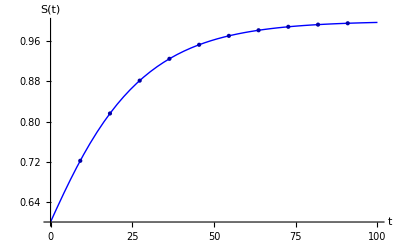

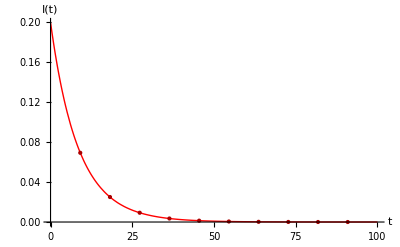

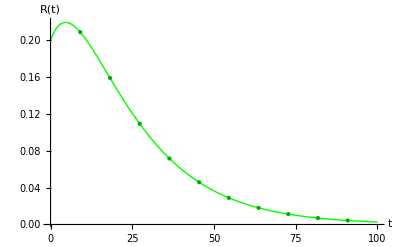

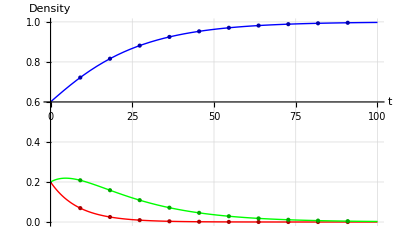

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=μ*n+ν*r[t]-μ*s[t]-β * s[t]* i[t]/n;
eq2=β*s[t]*i[t]/n-μ*i[t]-γ*i[t];
eq3=γ*i[t]-μ*r[t]-ν*r[t];
n=1;
β=0.04;
γ=0.1;
μ=0.043;
ν=0.01;
R0=N[β/(γ+μ)]
tf=100;
szero=0.6;
izero=0.2;
rzero=0.2;

sol=NDSolve[{s'[t]==eq1,i'[t]==eq2,r'[t]==eq3,s[0]==szero,i[0]==izero,r[0]==rzero},{s,i,r},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For I[t] versus t *)
plot2a=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"R"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For R[t] versus t *)
plot3a=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"},{Graphics[{Green,Line[{{0,0},{1,0}}]}],"R(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[i[t]/.sol],Evaluate[r[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","I(t)","R(t)"}, PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

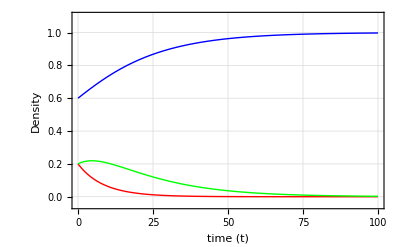

1.6

0.625

0.125

0.25

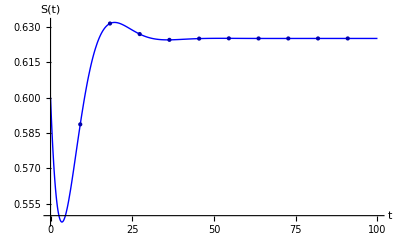

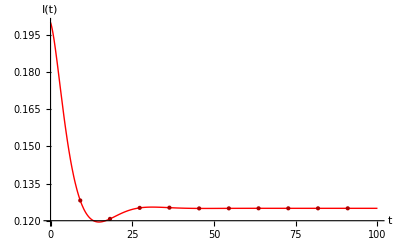

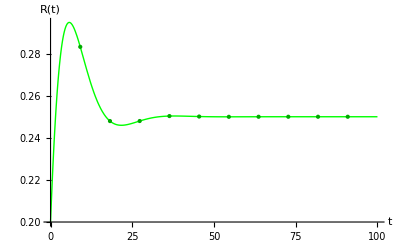

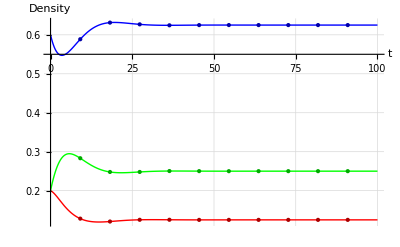

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=μ*n+ν*r[t]-μ*s[t]-β * s[t]* i[t]/n;
eq2=β*s[t]*i[t]/n-μ*i[t]-γ*i[t];
eq3=γ*i[t]-μ*r[t]-ν*r[t];
n=1;
β=0.8;
γ=0.4;
μ=0.1;
ν=0.1;
R0=β/(γ+μ)
St=n/R0
It=(n(μ+γ) (μ+ν)(R0-1))/(β (μ+γ+ν))
Rt=(n γ (μ+γ) (R0-1))/(β (μ+γ+ν))
tf=100;
szero=0.6;
izero=0.2;
rzero=0.2;

sol=NDSolve[{s'[t]==eq1,i'[t]==eq2,r'[t]==eq3,s[0]==szero,i[0]==izero,r[0]==rzero},{s,i,r},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For I[t] versus t *)
plot2a=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"R"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For R[t] versus t *)
plot3a=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"},{Graphics[{Green,Line[{{0,0},{1,0}}]}],"R(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[i[t]/.sol],Evaluate[r[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","I(t)","R(t)"}, PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

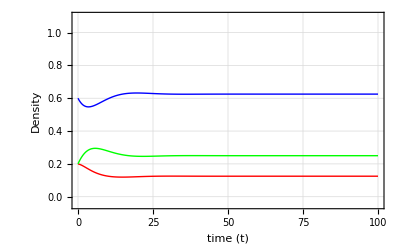

```mathematica
Clear["Global`*"]
β=0.8;
μ=0.1;
γ=0.4;
ν=0.1;

λ1=-(μ+ν);
λ2=β-μ-γ;

r0=β/(μ+γ)

e1={1,0}
e2={1/r0, ((μ+γ) (μ+ν) (r0-1))/(β (μ+γ+ν)), (γ(μ+γ) (r0-1))/(β (μ+γ+ν))};
(*ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;
*)
δ=0.15;
VectorPlot[{-β s i/1-μ s+μ+ν (1-s-i), β s i/1-γ i-μ i},{s,e1[[1]]-δ,e1[[1]]+δ},{i,e1[[2]]-δ,e1[[2]]+δ},VectorScale->{Automatic,Automatic,None},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

1.6

{1,0}

0.27972

{3.575,-0.891993,-1.68301}

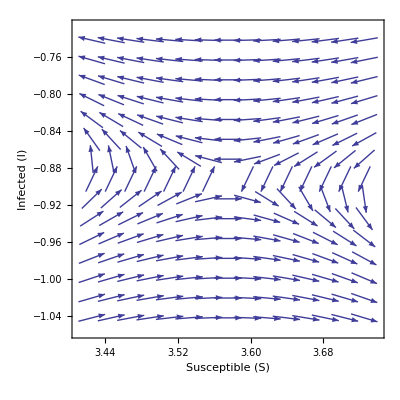

```mathematica
Clear["Global`*"]
β=0.04;
μ=0.043;
γ=0.1;
ν=0.01;

λ1=-μ;
λ2=-(β-μ-γ);

r0=β/(μ+γ)

e1={1,0};
e2={1/r0, ((μ+γ) (μ+ν) (r0-1))/(β (μ+γ+ν)), (γ(μ+γ) (r0-1))/(β (μ+γ+ν))}
(*ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;
*)
δ=0.15;
VectorPlot[{-β s i/1-μ s+μ+ν (1-s-i), β s i/1-γ i-μ i},{s,e2[[1]]-δ,e2[[1]]+δ},{i,e2[[2]]-δ,e2[[2]]+δ},VectorScale->{Automatic,Automatic,None},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

1.6

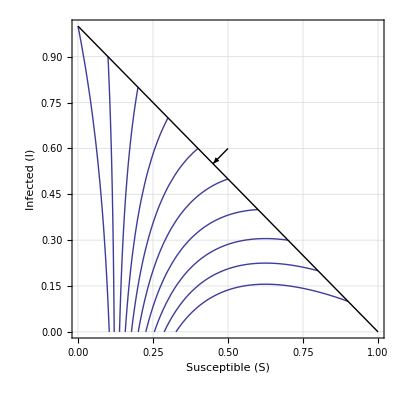

```mathematica
(*This is example of Tunnel Diode Example*)
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=μ n-μ s[t]-ν (n-s[t]-i[t]) - β * s[t]*i[t]/n;
eq2=β*s[t]*i[t]/n-(μ+γ)*i[t];

n=1;
β=0.8;
μ=0.1;
γ=0.4;
ν=0.1;

R0=N[β/(γ+μ)]
St=n/R0;
It=(n μ (R0-1))/β;
tf=50;
num=10;

szero[0]=1.0;
izero[0]=0.0;
rzero[0]=0.0;

szero[1]=0.9;
izero[1]=0.1;
rzero[1]=0.0;

szero[2]=0.8;
izero[2]=0.2;
rzero[2]=0.0;

szero[3]=0.7;
izero[3]=0.3;
rzero[3]=0.0;

szero[4]=0.6;
izero[4]=0.4;
rzero[4]=0.0;

szero[5]=0.5;
izero[5]=0.5;
rzero[5]=0.0;

szero[6]=0.4;
izero[6]=0.6;
rzero[6]=0.0;

szero[7]=0.3;
izero[7]=0.7;
rzero[7]=0.0;

szero[8]=0.2;
izero[8]=0.8;
rzero[8]=0.0;

szero[9]=0.1;
izero[9]=0.9;
rzero[9]=0.0;

szero[10]=0.0;
izero[10]=1.0;
rzero[10]=0.0;


Do[sol[k]=NDSolve[{s'[t]==eq1,i'[t]==eq2, s[0]==szero[k],i[0]==izero[k]},{s,i},{t,tf}],{k,0,num}]


pl[k_]:=ParametricPlot[Evaluate[{s[t],i[t]}/.sol[k]],{t,0,tf},PlotRange->All]

pls=Flatten[Table[pl[k],{k,0,num}]];
line = Graphics[Line[{{0,1.0},{1.0,0}}]];
arrow=Graphics[{Arrowheads[0.03],Arrow[{{0.5,0.6},{0.45,0.55}}]}];
pic1=Show[pls,line,arrow,PlotRange->{{0.0,1.0},{0.0,1.0}},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

1.6

{0.625,0.125,0.25}

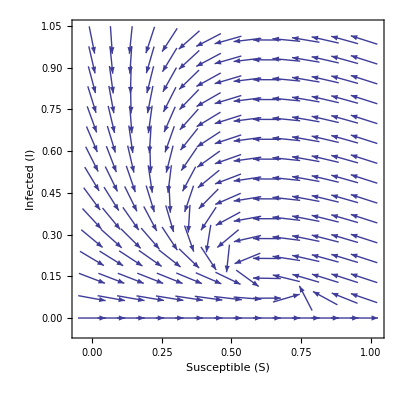

```mathematica
Clear["Global`*"]
β=0.8;
μ=0.1;
γ=0.4;
ν=0.1;

λ1=-μ;
λ2=-(β-μ-γ);

r0=β/(μ+γ)
Subscript[c, 1]=(ν+μ)/(γ+ν+μ);
Subscript[c, 2]=γ/(γ+ν+μ);

e1={1,0};
e2={1/r0, 1/r0 Subscript[c, 1] (r0-1), 1/r0 Subscript[c, 2] (r0-1)}
(*ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;
*)
δ=0.15;
VectorPlot[{-β s i/1-μ s+μ+ν (1-s-i), β s i/1-γ i-μ i},{s,e1[[1]]-1,e1[[1]]-0.025},{i,e1[[2]],e1[[2]]+1},VectorScale->{Automatic,Automatic,None},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

0.27972

{3.575,-0.891993,-1.68301}

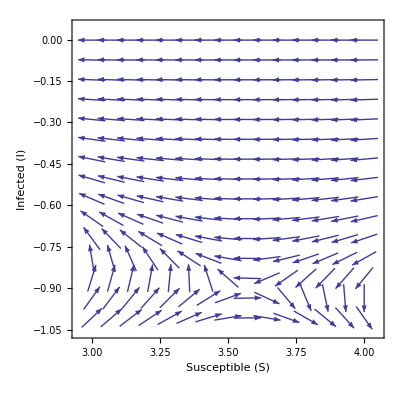

```mathematica
Clear["Global`*"]
β=0.04;
μ=0.043;
γ=0.1;
ν=0.01;

λ1=-μ;
λ2=-(β-μ-γ);

r0=β/(μ+γ)
Subscript[c, 1]=(ν+μ)/(γ+ν+μ);
Subscript[c, 2]=γ/(γ+ν+μ);

e1={1,0};
e2={1/r0, 1/r0 Subscript[c, 1] (r0-1), 1/r0 Subscript[c, 2] (r0-1)}
(*ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;
*)
δ=0.115;
VectorPlot[{-β s i/1-μ s+μ+ν (1-s-i), β s i/1-γ i-μ i},{s,e2[[1]]-0.575,e2[[1]]+(4-3.575)},{i,e2[[2]]-δ,e2[[2]]+0.89},VectorScale->{Automatic,Automatic,None},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

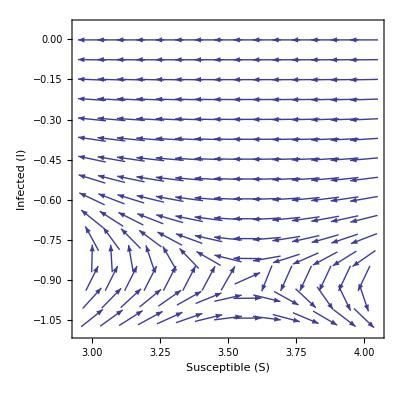
```mathematica
-Graphics--Graphics-
```

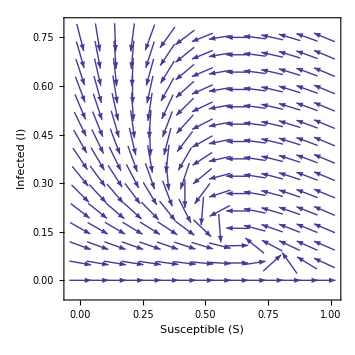

```mathematica
Clear["Global`*"]
eqS=μ n+ν r-β s i/n-μ s;
eqI=β s i/n-(μ+γ)i;
eqR=γ i -(μ+ν)r;
sumEq=s+i+r;
sol=Solve[eqS==0&&eqI==0&&eqR==0&&sumEq==n,{s,i,r}]
eqS=eqS/.{r->n-s-i}
MatrixForm[({{D[eqS,s], D[eqS,i]}, {D[eqI,s], D[eqI,i]}})]
Jaco=({{D[eqS,s], D[eqS,i]}, {D[eqI,s], D[eqI,i]}})/.sol
MatrixForm[Jaco[[1]]]
MatrixForm[Jaco[[2]]]
eigen1=FullSimplify[Eigenvalues[Jaco[[1]]]]
eigen2=FullSimplify[Eigenvalues[Jaco[[2]]]]
Reduce[eigen2[[1]]<0&&eigen2[[2]]<0&&μ>0&&β>0&&γ>0&&ν>0,{μ,β,γ,ν},Reals]
```

{{s→n,i→0,r→0},{s→(n (γ+μ))/β,i→(n (β-γ-μ) (μ+ν))/(β (γ+μ+ν)),r→-(n γ (-β+γ+μ))/(β (γ+μ+ν))}}

-(i s β)/n+n μ-s μ+(-i+n-s) ν

(-(i β)/n-μ-ν | -(s β)/n-ν
(i β)/n | (s β)/n-γ-μ)

{{{-μ-ν,-β-ν},{0,β-γ-μ}},{{-μ-ν-((β-γ-μ) (μ+ν))/(γ+μ+ν),-γ-μ-ν},{((β-γ-μ) (μ+ν))/(γ+μ+ν),0}}}

(-μ-ν | -β-ν
0 | β-γ-μ)

(-μ-ν-((β-γ-μ) (μ+ν))/(γ+μ+ν) | -γ-μ-ν
((β-γ-μ) (μ+ν))/(γ+μ+ν) | 0)

{β-γ-μ,-μ-ν}

```mathematica
s1={-1/(2 (γ+μ+ν))((β+ν) (μ+ν)+√(μ+ν) √(-4 β (γ+μ)^2+4 (γ+μ)^3+8 (γ+μ)^2 ν-2 β (4 γ+3 μ) ν-2 β ν^2+(4 γ+5 μ) ν^2+ν^3+β^2 (μ+ν))),1/(2 (γ+μ+ν))(-(β+ν) (μ+ν)+√(μ+ν) √(-4 β (γ+μ)^2+4 (γ+μ)^3+8 (γ+μ)^2 ν-2 β (4 γ+3 μ) ν-2 β ν^2+(4 γ+5 μ) ν^2+ν^3+β^2 (μ+ν)))}
```

{-((β+ν) (μ+ν)+√(μ+ν) √(-4 β (γ+μ)^2+4 (γ+μ)^3+8 (γ+μ)^2 ν-2 β (4 γ+3 μ) ν-2 β ν^2+(4 γ+5 μ) ν^2+ν^3+β^2 (μ+ν)))/(2 (γ+μ+ν)),((-β-ν) (μ+ν)+√(μ+ν) √(-4 β (γ+μ)^2+4 (γ+μ)^3+8 (γ+μ)^2 ν-2 β (4 γ+3 μ) ν-2 β ν^2+(4 γ+5 μ) ν^2+ν^3+β^2 (μ+ν)))/(2 (γ+μ+ν))}

```mathematica
FullSimplify[s1[[1]]]
```

-((β+ν) (μ+ν)+√(μ+ν) √(-4 β (γ+μ)^2+4 (γ+μ)^3+8 (γ+μ)^2 ν-2 β (4 γ+3 μ) ν-2 β ν^2+(4 γ+5 μ) ν^2+ν^3+β^2 (μ+ν)))/(2 (γ+μ+ν))

```mathematica
δ=(β+ν) (μ+ν)
```

(β+ν) (μ+ν)

```mathematica
χ=-4 β (γ+μ)^2+4 (γ+μ)^3+8 (γ+μ)^2 ν-2 β (4 γ+3 μ) ν-2 β ν^2+(4 γ+5 μ) ν^2+ν^3+β^2 (μ+ν);
χ=χ(μ+ν)
```

(μ+ν) (-4 β (γ+μ)^2+4 (γ+μ)^3+8 (γ+μ)^2 ν-2 β (4 γ+3 μ) ν-2 β ν^2+(4 γ+5 μ) ν^2+ν^3+β^2 (μ+ν))

```mathematica
δ^2
```

(β+ν)^2 (μ+ν)^2

```mathematica
Reduce[δ^2>χ&&μ>0&&β>0&&γ>0&&ν>0,{μ,β,γ,ν},Reals]
```

μ>0&&β>μ&&0<γ<β-μ&&ν>0

```mathematica
Reduce[(μ+ν)(-4 β (γ+μ)^2+4 (γ+μ)^3+8 (γ+μ)^2 ν-2 β (4 γ+3 μ) ν-2 β ν^2+(4 γ+5 μ) ν^2+ν^3+β^2 (μ+ν))]
```

Reduce[(μ+ν) (-4 β (γ+μ)^2+4 (γ+μ)^3+8 (γ+μ)^2 ν-2 β (4 γ+3 μ) ν-2 β ν^2+(4 γ+5 μ) ν^2+ν^3+β^2 (μ+ν))]